# Condiciones de singularidad

## Solución general de tercer orden en la curvatura

```mathematica
f3gen=Assuming[r>0&&μ>0&&r^4>0&&α>0&&β>0,-(-7 r^2 α-36 β^2)/(36 β^2)-(-49 r^4 α^2+756 r^4 β^2)/(18 2^(2/3) β^2 (686 r^6 α^3-15876 r^6 α β^2-27216 r^2 α β^4-27216 r^2 β^4 μ+√(4 (-49 r^4 α^2+756 r^4 β^2)^3+(686 r^6 α^3-15876 r^6 α β^2-27216 r^2 α β^4-27216 r^2 β^4 μ)^2))^(1/3))+1/(36 2^(1/3) β^2)(686 r^6 α^3-15876 r^6 α β^2-27216 r^2 α β^4-27216 r^2 β^4 μ+√(4 (-49 r^4 α^2+756 r^4 β^2)^3+(686 r^6 α^3-15876 r^6 α β^2-27216 r^2 α β^4-27216 r^2 β^4 μ)^2))^(1/3)]
```

-(-7 r^2 α-36 β^2)/(36 β^2)-(-49 r^4 α^2+756 r^4 β^2)/(18 2^(2/3) β^2 (686 r^6 α^3-15876 r^6 α β^2-27216 r^2 α β^4-27216 r^2 β^4 μ+√(4 (-49 r^4 α^2+756 r^4 β^2)^3+(686 r^6 α^3-15876 r^6 α β^2-27216 r^2 α β^4-27216 r^2 β^4 μ)^2))^(1/3))+((686 r^6 α^3-15876 r^6 α β^2-27216 r^2 α β^4-27216 r^2 β^4 μ+√(4 (-49 r^4 α^2+756 r^4 β^2)^3+(686 r^6 α^3-15876 r^6 α β^2-27216 r^2 α β^4-27216 r^2 β^4 μ)^2))^(1/3))/(36 2^(1/3) β^2)

```mathematica
Clear[α,β,μ]
μ:=1
Manipulate[Plot[-(-7 r^2 α-36 β^2)/(36 β^2)-(-49 r^4 α^2+756 r^4 β^2)/(18 2^(2/3) β^2 (686 r^6 α^3-15876 r^6 α β^2-27216 r^2 α β^4-27216 r^2 β^4 μ+√(4 (-49 r^4 α^2+756 r^4 β^2)^3+(686 r^6 α^3-15876 r^6 α β^2-27216 r^2 α β^4-27216 r^2 β^4 μ)^2))^(1/3))+1/(36 2^(1/3) β^2)(686 r^6 α^3-15876 r^6 α β^2-27216 r^2 α β^4-27216 r^2 β^4 μ+√(4 (-49 r^4 α^2+756 r^4 β^2)^3+(686 r^6 α^3-15876 r^6 α β^2-27216 r^2 α β^4-27216 r^2 β^4 μ)^2))^(1/3),{r,0,6},AxesLabel->{"r","f(r)"},PlotRange->All],{α,-0.1,0.1,0.002},{β,-0.05,0.05,0.001}]
```

```mathematica
Clear[μ]
```

#### Ceros de la función

```mathematica
Solve[f3gen==0,r,Reals]
```

{{r→ConditionalExpression[-√Root[144 β^4-168 β^2 μ #1+(504 β^2+49 μ^2) #1^2-294 μ #1^3+441 #1^4&,1], ]},{r→ConditionalExpression[√Root[144 β^4-168 β^2 μ #1+(504 β^2+49 μ^2) #1^2-294 μ #1^3+441 #1^4&,1], ]},{r→ConditionalExpression[-√Root[144 β^4-168 β^2 μ #1+(504 β^2+49 μ^2) #1^2-294 μ #1^3+441 #1^4&,3], ]},{r→ConditionalExpression[√Root[144 β^4-168 β^2 μ #1+(504 β^2+49 μ^2) #1^2-294 μ #1^3+441 #1^4&,3], ]}}

```mathematica
ToRadicals[√Root[144 β^4-168 β^2 #1+(49+504 β^2) #1^2-294 #1^3+441 #1^4&,1]]
```

(√(7-√7 √(7-144 β^2)))/(√42)

```mathematica
ToRadicals[√Root[144 β^4-168 β^2 #1+(49+504 β^2) #1^2-294 #1^3+441 #1^4&,3]]
```

(√(7+√7 √(7-144 β^2)))/(√42)

### Denominador

```mathematica
dem:=686 r^6 α^3-15876 r^6 α β^2-27216 r^2 β^4-27216 r^2 α β^4+√(4 (-49 r^4 α^2+756 r^4 β^2)^3+(686 r^6 α^3-15876 r^6 α β^2-27216 r^2 β^4-27216 r^2 α β^4)^2)
```

```mathematica
Solve[dem==0,β]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{β→-1/6 √(7/3) α},{β→1/6 √(7/3) α}}

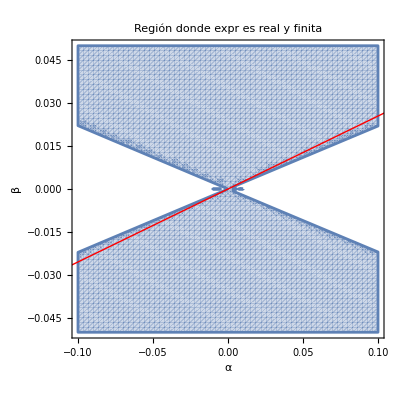

```mathematica
μ:=1
r:=1
RegionPlot[Im[dem]==0&&dem!=0,{α,-0.1,0.1},{β,-0.05,0.05},PlotPoints->60,FrameLabel->{"α","β"},PlotLabel->"Región donde expr es real y finita",Epilog->{Thick,Red,InfiniteLine[{{0,0},{1,Sqrt[7/108]}}]}]
Clear[μ,r]
```

### ¿Cómo se comporta f(r) en r -> Infinito?

```mathematica
Assuming[r>0&& α>0 &&β>0,Simplify[Series[Simplify[f3gen],{r,Infinity,2}]]]
```

((7 α+(7^(2/3) (7 α^2-108 β^2))/((49 α^3-1134 α β^2+54 √21 β^2 √(-7 α^2+144 β^2))^(1/3))+7^(1/3) (49 α^3-1134 α β^2+54 √21 β^2 √(-7 α^2+144 β^2))^(1/3)) r^2)/(36 β^2)+1+((-1134 α^2 β^2+23328 β^4+7 √21 α^3 √(-7 α^2+144 β^2)-162 √21 α β^2 √(-7 α^2+144 β^2)) (-7 7^(2/3) α^2+108 7^(2/3) β^2+7^(1/3) (49 α^3-1134 α β^2+54 √21 β^2 √(-7 α^2+144 β^2))^(2/3)) (α+μ))/(9 (7 α^2-144 β^2) (49 α^3-1134 α β^2+54 √21 β^2 √(-7 α^2+144 β^2))^(4/3) r^2)+O[1/r]^3

```mathematica
CoefCuad:= 1/(36 β^2)(7 α+(7^(2/3) (7 α^2-108 β^2))/((49 α^3-1134 α β^2+54 √21 β^2 √(-7 α^2+144 β^2))^(1/3))+7^(1/3) (49 α^3-1134 α β^2+54 √21 β^2 √(-7 α^2+144 β^2))^(1/3))
```

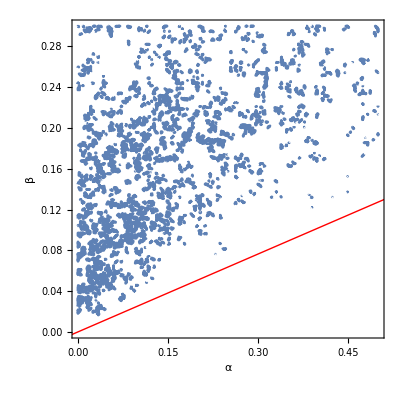

```mathematica
Assuming[α>0 &&β>0,RegionPlot[CoefCuad==0,{α,0,0.5},{β,0,0.3},PlotPoints->60,FrameLabel->{"α","β"},Epilog->{Thick,Red,InfiniteLine[{{0,0},{1,Sqrt[7/108]}}]}]]
```

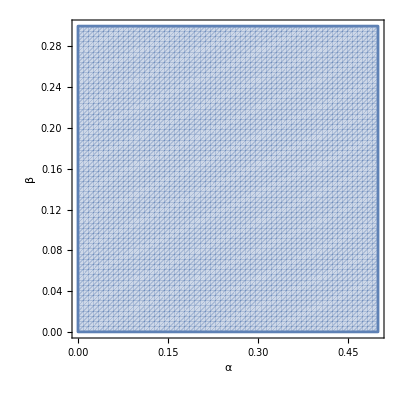

```mathematica
Assuming[α>0 &&β>0,RegionPlot[((-1134 α^2 β^2+23328 β^4+7 √21 α^3 √(-7 α^2+144 β^2)-162 √21 α β^2 √(-7 α^2+144 β^2)) (-7 7^(2/3) α^2+108 7^(2/3) β^2+7^(1/3) (49 α^3-1134 α β^2+54 √21 β^2 √(-7 α^2+144 β^2))^(2/3)) )/(9 (7 α^2-144 β^2) (49 α^3-1134 α β^2+54 √21 β^2 √(-7 α^2+144 β^2))^(4/3))!=0,{α,0,0.5},{β,0,0.3},PlotPoints->60,FrameLabel->{"α","β"}]]
```

### ¿Cómo se comporta f(r) en r->0?

```mathematica
Assuming[r>0&&α>0&&β>0&&μ>0,Simplify[Series[Simplify[f3gen],{r,0,2}]]]
```

1+((7/3)^(1/3) (7 α^2-108 β^2) r^(2/3))/(2^(2/3) β^(2/3) (((-7 α^2+108 β^2)^3)/(α+μ))^(1/3))+(7 α r^2)/(36 β^2)+O[r]^(7/3)

```mathematica
G[α_,β_,μ_]:=((7/3)^(1/3) (-α-μ+√((α+μ)^2))^(1/3))/(2 β^(2/3))
```

```mathematica
Solve[G[α,β,μ]==0,α]
```

{{}}

### Condiciones para que haya dos raíces

```mathematica
df3:=Simplify[D[f3gen,r]]
```

```mathematica
Assuming[r>0&&β>0,Simplify[Series[Simplify[df3],{r,0,1}]]]
```

((7/3)^(1/3) (-α-μ+√((α+μ)^2))^(1/3))/(3 β^(2/3) r^(1/3))+(7 α r)/(18 β^2)+O[r]^(4/3)

```mathematica
Simplify[((7/3)^(1/3) (-α-μ+√((α+μ)^2))^(1/3))/(3 β^(2/3))/G[α,β,μ]]
```

2/3

```mathematica
μ:=1
RegionPlot[G[α,β,μ]<0,{α,-0.1,0.1},{β,-0.05,0.05},PlotPoints->40,FrameLabel->{"α","β"}]
```

-Graphics-

```mathematica
Clear[μ]
```

```mathematica
G[α,β,μ]
```

((7/3)^(1/3) (-α-μ+√((α+μ)^2))^(1/3))/(2 β^(2/3))

### Invariante de Kretschmann

```mathematica
NN[r_]:=1
f[r_]:=f3gen
Krt[r_]=Simplify[-1/(r^4 NN[r]^2)(9 r^4 f'[r]^2 NN'[r]^2+6 r^4 NN[r] f'[r] NN'[r] f''[r]+NN[r]^2 (12-24 f[r]+12 f[r]^2+6 r^2 f'[r]^2+r^4 f''[r]^2)+12 r^4 f[r] f'[r] NN'[r] NN''[r]+4 f[r] NN[r] (3 r^2 f'[r] NN'[r]+r^4 f''[r] NN''[r])+4 f[r]^2 (3 r^2 NN'[r]^2+r^4 NN''[r]^2))]
```

-((7 7^(2/3) r^4 α^2-108 7^(2/3) r^4 β^2+7 r^2 α (7 r^6 (7 α^3-162 α β^2)-1944 r^2 β^4 (α+μ)+18 √3 √(r^4 β^4 (-63 r^8 (7 α^2-144 β^2)-28 r^4 α (7 α^2-162 β^2) (α+μ)+3888 β^4 (α+μ)^2)))^(1/3)+7^(1/3) (7 r^6 (7 α^3-162 α β^2)-1944 r^2 β^4 (α+μ)+18 √3 √(r^4 β^4 (-63 r^8 (7 α^2-144 β^2)-28 r^4 α (7 α^2-162 β^2) (α+μ)+3888 β^4 (α+μ)^2)))^(2/3))^2/(108 r^4 β^4 (7 r^6 (7 α^3-162 α β^2)-1944 r^2 β^4 (α+μ)+18 √3 √(r^4 β^4 (-63 r^8 (7 α^2-144 β^2)-28 r^4 α (7 α^2-162 β^2) (α+μ)+3888 β^4 (α+μ)^2)))^(2/3)))

kretschmann en r que tiende a infinito

```mathematica
Assuming[r>0,Simplify[Series[Simplify[Krt[r]],{r,Infinity,1}]]]
```

-((7 7^(2/3) α^2-108 7^(2/3) β^2+7 α (49 α^3-1134 α β^2+54 √21 √(-7 α^2 β^4+144 β^6))^(1/3)+7^(1/3) (49 α^3-1134 α β^2+54 √21 √(-7 α^2 β^4+144 β^6))^(2/3))^2)/(108 (β^4 (49 α^3-1134 α β^2+54 √21 √(-7 α^2 β^4+144 β^6))^(2/3)))+O[1/r]^2

kretschmann en r que tiende a 0

```mathematica
Assuming[r>0&&(α+μ)>0&&β>0,Simplify[Series[Simplify[Krt[r]],{r,0,1}]]]
```

(3^(1/3) 14^(2/3) (((-7 α^2+108 β^2)^3 (α+μ)^2)/β^4)^(1/3))/((7 α^2-108 β^2) r^(8/3))-(7 ((14/3)^(1/3) α (7 α^2-108 β^2)))/(3 (β^(8/3) (((-7 α^2+108 β^2)^3)/(α+μ))^(1/3)) r^(4/3))+(7 (-7 α^2+72 β^2))/(36 β^4)+O[r]^(4/3)

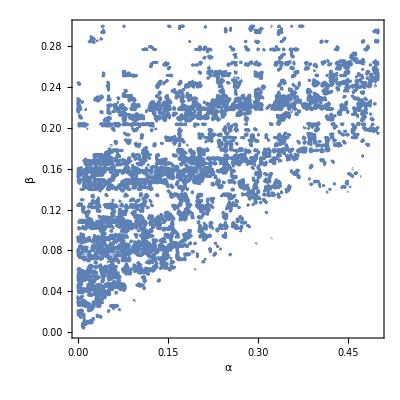

```mathematica
Assuming[α>0 &&β>0,RegionPlot[((7 7^(2/3) α^2-108 7^(2/3) β^2+7 α (49 α^3-1134 α β^2+54 √21 √(-7 α^2 β^4+144 β^6))^(1/3)+7^(1/3) (49 α^3-1134 α β^2+54 √21 √(-7 α^2 β^4+144 β^6))^(2/3))^2)/(108 (β^4 (49 α^3-1134 α β^2+54 √21 √(-7 α^2 β^4+144 β^6))^(2/3)))==0,{α,0,0.5},{β,0,0.3},PlotPoints->60,FrameLabel->{"α","β"}]]
```

```mathematica
μ:=1
Plot3D[(3^(1/3) 14^(2/3) (((-7 α^2+108 β^2)^3 (α+μ)^2)/β^4)^(1/3))/((7 α^2-108 β^2) r^(8/3))-(7 ((14/3)^(1/3) α (7 α^2-108 β^2)))/(3 (β^(8/3) (((-7 α^2+108 β^2)^3)/(α+μ))^(1/3)) r^(4/3))+(7 (-7 α^2+72 β^2))/(36 β^4)/.r->1,{α,-0.5,0.5},{β,-0.3,0.3},PlotRange->{-1,1},AxesLabel->{"α","β","f(α, β, 1)"},ColorFunction->"ThermometerColors",Mesh->None,PlotPoints->60]
```

-Graphics3D-

```mathematica
Plot3D[Krt[0.025],{α,0,1},{β,0,0.5},PlotRange->{-5,5},AxesLabel->{"α","β","Krt"},ColorFunction->"ThermometerColors",Mesh->None,PlotPoints->60]
```

-Graphics3D-

```mathematica
Plot3D[((7 7^(2/3) α^2-108 7^(2/3) β^2+7 α (49 α^3-1134 α β^2+54 √21 √(-7 α^2 β^4+144 β^6))^(1/3)+7^(1/3) (49 α^3-1134 α β^2+54 √21 √(-7 α^2 β^4+144 β^6))^(2/3))^2)/(108 (β^4 (49 α^3-1134 α β^2+54 √21 √(-7 α^2 β^4+144 β^6))^(2/3))),{α,0,1},{β,0,0.5},PlotRange->{-5,5},AxesLabel->{"α","β","Krt"},ColorFunction->"ThermometerColors",Mesh->None,PlotPoints->60]
```

-Graphics3D-

```mathematica
Assuming[r>0&&α>0&&β>0,Series[f3gen,{α,0,2},{β,0,2}]]
```

((1-1/(3 r^2))+(4 β^2)/(189 r^10)+O[β]^3)+((1-9 r^4)/(27 r^6)+(4 (-5+27 r^4) β^2)/(1701 r^14)+O[β]^3) α+((2 (-1+9 r^4))/(243 r^10)+(4 (7-60 r^4+81 r^8) β^2)/(5103 r^18)+O[β]^3) α^2+O[α]^3